```mathematica
file = "C:\\Users\\fskdm\\Projects\\sa-coronavirus-2020\\time_series_covid19_confirmed_global.txt"
data = Import["C:\\Users\\fskdm\\Projects\\sa-coronavirus-2020\\time_series_covid19_confirmed_global.txt", "CSV"]
```

C:\Users\fskdm\Projects\sa-coronavirus-2020\time_series_covid19_confirmed_global.txt

{1}
 |  |  |  |

```mathematica
data[[5, 1;;]]
```

{,Andorra,42.5063,1.5218,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,39,39,53,75,88,113,133,164,188,224,267,308,334,370,376,390,428}

```mathematica
data[[5, 2]]
```

Andorra

```mathematica
it =Select[data, #[[2]]== "Italy"&]
```

{{,Italy,43.,12.,0,0,0,0,0,0,0,0,0,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,20,62,155,229,322,453,655,888,1128,1694,2036,2502,3089,3858,4636,5883,7375,9172,10149,12462,12462,17660,21157,24747,27980,31506,35713,41035,47021,53578,59138,63927,69176,74386,80589,86498,92472,97689,101739,105792,110574,115242}}

```mathematica
za=Select[data, #[[2]]== "South Africa"&]
```

{{,South Africa,-30.5595,22.9375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,3,3,7,13,17,24,38,51,62,62,116,150,202,240,274,402,554,709,927,1170,1187,1280,1326,1353,1380,1462}}

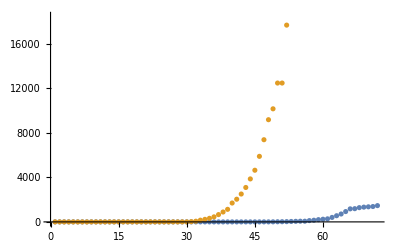

```mathematica
ListPlot[{za[[1,5;;]], it[[1,5;;]]}, PlotRange->Automatic]
```

```mathematica
zaT = TimeSeries[Transpose[Join[{data[[1,5;;]]},{za[[1,5;;]]}]]]
```

AbsoluteTime::ambig: Warning: the interpretation of the string 2/1/20 as a date is ambiguous.

AbsoluteTime::ambig: Warning: the interpretation of the string 2/2/20 as a date is ambiguous.

AbsoluteTime::ambig: Warning: the interpretation of the string 2/3/20 as a date is ambiguous.

General::stop: Further output of AbsoluteTime::ambig will be suppressed during this calculation.

TimeSeries[…]

```mathematica
itT = TimeSeries[Transpose[Join[{data[[1,5;;]]},{it[[1,5;;]]}]]]
```

AbsoluteTime::ambig: Warning: the interpretation of the string 2/1/20 as a date is ambiguous.

AbsoluteTime::ambig: Warning: the interpretation of the string 2/2/20 as a date is ambiguous.

AbsoluteTime::ambig: Warning: the interpretation of the string 2/3/20 as a date is ambiguous.

General::stop: Further output of AbsoluteTime::ambig will be suppressed during this calculation.

TimeSeries[…]

```mathematica
eventstring = "2020-03-8\t5\t4000\tItaly Lockdown 
2020-03-15\t11\t2000\tState of Disaster
2020-03-26\t22\t5000\tSA Lockdown";
eventdata = ImportString[eventstring, "TSV"]
```

{{2020-03-8,5,4000,Italy Lockdown},{2020-03-15,11,2000,State of Disaster},{2020-03-26,22,5000,SA Lockdown}}

```mathematica
eventsT = TimeSeries[eventdata[[All, {1,3}]]]
```

```mathematica
TimeSeries[…]
```

TimeSeries[…]

```mathematica
events = {}
```

```mathematica
exportimage=DateListPlot[{zaT, itT, Map[Callout[#[[{1,3}]],#[[4]]]&, eventdata]}
, DateTicksFormat->{"Day", " ", "MonthNameShort"}
, Joined->{True, True, False}
, ImageSize->800
, PlotLabel->Style["COVID-19 Cases and Lockdown\nItaly and South Africa", Bold, Medium, Black]
, PlotRange->Automatic
, Frame->True
, FrameLabel->{"Date", "Cases"}
, FrameStyle->Directive[Black, Medium, Bold]
, PlotLegends->{"South Afria","Italy", "Events"}
, Filling->{3-> Axis}
, FillingStyle->Directive[Thickness[.01]]
]
```

-Graphics-

```mathematica
exportfile = "C:\\Users\\fskdm\\Projects\\sa-coronavirus-2020\\2020_04_03_SA_Italy_Lockdown.png"
```

C:\Users\fskdm\Projects\sa-coronavirus-2020\2020_04_03_SA_Italy_Lockdown.png

```mathematica
Export[exportfile, exportimage]
```

C:\Users\fskdm\Projects\sa-coronavirus-2020\2020_04_03_SA_Italy_Lockdown.png